# Predicting Mountains’ Locations

## A program to classify the position of a given mountain by its elevation data

Lena Libon
Harshal Gajjar

Mountains have a huge impact on weather and climate conditions and are important landmarks. The aim of my project was to classify the position of a mountain using its elevation data as an input.

## Project Description

My final program classifies the country of a given mountain using its elevation data as an input.The data is sent to a neural network, which was trained on the elevation data of the five highest mountains per country in Europe. Then, the program returns a map displaying the location of the mountains. 
Another neural network, trained on the ReliefPlot of the ten highest mountains per continent, identifies the continent to which the elevation data belong and then plots the probabilities of a mountain belonging to the continents using a map with different colors. However, this method is more time consuming because of the data size.
The third approach is to recognize a mountain by its profile which you can easily create by using the ListPlot3D function.

## Overview

To implement this project, I had three different approaches, of which one turned out to be the most efficient one.
I started by 3D-Plotting the ten highest mountains in the world, editing the plot and then fitting pictures from different viewpoints of the mountains to a neural network. Thereby, the mountains are identified by their profile. In order to train a useful neural network, a great amount of data is required. This means that you have to create many slightly different pictures by changing the GeoRange, which is the length of the shown part, and the viewpoints, which are the angles from where you look at the mountains. This method did not turn out to be useful, because the performance of my computer could not compete with the requirements in terms of required number of graphics in a reasonable amount of time. 

Another way to accomplish the project was to train a neural network by using the surface plots of the mountains. I trained the network on the ten highest mountains of each continent. To create more data, I changed the GeoRange and the center of the plot to up to 100 feet to the east. The respective result is promising. By using GeoElevationData as input data, the program returns the respective probabilities for the continents, which are then illustrated on a map. However, similar to the first approach, memory problems of my computer occurred when creating more data and considering the 5 highest mountains for each country. 

The simplest way to handle the problem is to use only the GeoElevationData. In my third approach, I implemented this strategy by specializing on the five highest mountains of all countries in Europe. Therefore, I created data, which were varied by different GeoRanges, by shifting the center of the graphic up to 100 meters to the east.

## Settings

Change the current directory to the WorkDirectory.

```mathematica
SetDirectory[$WorkDirectory];
(* change the directory *)
```

## Recognizing a mountain by its profile

### Plotting the surface of a mountain

First, I create an example picture of the Mount Everest. I don’t want to have a box around the plot, neither a mesh, axes or a boundary. In addition, the size of the image should be medium and I want to look at the mountain from the front-perspective.

```mathematica
ListPlot3D[
	Reverse[
		GeoElevationData[WolframAlphaQueryParseResults, GeoRange-> WolframAlphaQueryParseResults, GeoProjection->Automatic]
	], ViewPoint-> Front, Axes-> False, Mesh->None, BoundaryStyle->None, Boxed->False, ImageSize->Medium] //Rasterize 
(* Create an example picture of the Mount Everest*)
```

-Graphics-

Because the ViewPoint  should not always be the front (I want to look at the mountain from different perspectives), I created a manipulated plot of the Mount Everest from which you can see the plot of all the positions of a circle surrounding the midpoint of the mountain.

```mathematica
Manipulate[
	Rasterize[
		ListPlot3D[
			Reverse[
				GeoElevationData[WolframAlphaQueryParseResults, GeoRange->WolframAlphaQueryParseResults, GeoProjection->Automatic]
			], Axes->False, Mesh->None, BoundaryStyle->None, Boxed->False, ViewPoint->{2 Cos[x], 2 Sin[x],0}]
		], {x, 0 , 2 Pi}]
(* Create a manipulate to see the mountain out of different view points *)
```

### Ten highest mountains of the world

I create a list of the ten highest mountains in the world by using the “Elevation”-EntityProperty:

```mathematica
TenHighestMountains = 
	Keys[
		EntityValue[
			EntityClass["Mountain", {EntityProperty["Mountain", "Elevation"]-> TakeLargest[10]}
		], EntityProperty["Mountain", "Elevation"], "EntityAssociation"]
	];
(* Create a list of the 10 highest mountains in the world *)
```

### Create a dataset of the rasterized pictures of the mountains

I create a list of the rasterized plots of the 10 highest mountains in the world. To get slightly different pictures, I vary the GeoRange and the ViewPoint. I also set the PlotStyle on black, change the lighting and fill the bottom black, so that the main focus is on its structure.

There are 41 * 5 * 4 = 820 different images created per mountain (all elements which are in the “TenHighestMountains” list.

That means that in total there are 820 * 10 = 8200 images. This is a good size to train the first model.

```mathematica
DatasetTenHighestMountains1 = 
	Flatten[
		Table[
			Rasterize[
				ListPlot3D[
					Reverse[
						GeoElevationData[
							TenHighestMountains⟦a⟧, GeoRange->Quantity[y,"Kilometers"], GeoProjection -> Automatic]
					], Axes->False, Mesh-> None, BoundaryStyle->None, Boxed->False, ImageSize->{224,224}, PlotStyle-> Black, Lighting -> {"Ambient", White}, Filling-> Bottom, FillingStyle-> Black, ViewPoint->{2 Cos[theta], 2 Sin[theta], z}]
			],{a,1,Length[TenHighestMountains]},{theta,0,2 Pi, 1/20 Pi},{y,4,20,4}, {z,0,0.7,0.2}
		]
	]
(* create a list of pictures of plotted mountains out of different viewpoints and with different georanges *)
```

This method is pretty time consuming, because every time a new plot is created, the GeoElevationData is downloaded again. As a result, I create a new function, which saves the elevation data and just changes the viewpoint for the mountains.

This function can be be achieved with the Show function which takes the earlier created plot and just changes the ViewPoint.

```mathematica
plotDatasetTenHighestMountains[mountain_, range_]:= 
	(plot = 
		ListPlot3D[
			Reverse[
				GeoElevationData[
					mountain, GeoRange->Quantity[
						range, "Kilometers"
					], GeoProjection->Automatic]
				], Mesh->None, ImageSize->{224, 224}, Boxed->False, Axes->False, BoundaryStyle->None, PlotStyle->Black, Lighting->{"Ambient", White}, Filling->Bottom, FillingStyle->Black]; 
		Table[
			Rasterize@Show[
				plot, ViewPoint-> {2 Cos[theta], 2 Sin[theta], z}
			], {theta, 0, 2 Pi, 1/20 Pi}, {z,0,0.7,0.2}
		]
	)
(* create a function which uses an earlier created plot and changes the ViewPoint *)
```

Now, I call this function.

```mathematica
DatasetTenHighestMountains2 = 
	Flatten[
		Table[
			plotDatasetTenHighestMountains[
				TenHighestMountains⟦x⟧, y
			], {x, 1, Length[TenHighestMountains]}, {y, 4, 20, 4}
		]
	];
(* create a list of pictures of plotted mountains out of different viewpoints and with different GeoRanges *)
```

Creating the data is not working for me, because of my computer’s memory. Nevertheless, in the following part,  I explain the way to proceed with this method if it is possible to create this dataset.

To train a model on the data, I need to have labels which associate with the created data in the list “DatasetTenHighestMountains2”:

I create the labels by looking how many pictures of plotted mountains I have in total in the list “DatasetTenHighestMountains2” and then divide that number by the number of elements in the list “TenHighestMountains” (the number of labels), which is 10. The result is the number of the pictures per mountain, that means the number of every name of the mountain has to be written behind each other in the order that corresponds to the order of the 10 highest mountains (this method only works, because there is always the same number of plots per mountain).

```mathematica
labelsTenHighestMountains = 
	Flatten[
		Table[
			Table[
				EntityValue[
					TenHighestMountains⟦a⟧, "Name"
				], (Length[DatasetTenHighestMountains2]/Length[TenHighestMountains])
			], {a, 1, Length[TenHighestMountains]}
		]
	];
(* create a list of the corresponding labels to the DatasetTenHighestMountains2 *)
```

To train a model on the data, the input needs to be an association between the images and their labels.

I have created the images and the labels in the equivalent order, so now I can match the nth plot with the nth label. You can do this by using the AssociationThread function. With the Normal-function, the association is converted into a list.

```mathematica
DatasetTenHighestMountains = 
	Normal[
		AssociationThread[
			DatasetTenHighestMountains2, labelsTenHighestMountains
		]
	];
(* create a list of associations between the plots and the matching labels *)
```

If you quit the kernel (e.g. close the window) you have to run the whole process again in order to get the dataset, that’s why it is useful to export important lists, etc. to a file, if you have once run the program. The file will be exported in your current directory:

You can get your current directory with:

```mathematica
Directory[]
(* get the current directory *)
```

Now export the list “DatasetTenHighestMountains”:

```mathematica
Export["DatasetTenHighestMountains.mx", DatasetTenHighestMountains];
```

### Create a classifier

In order to train the classifier in the best way, I scramble the data to prevent patterns :

```mathematica
scrambledDatasetTenHighestMountains = RandomSample@DatasetTenHighestMountains;
(* scramble the data *)
```

In order to test the real performance of the trained net, the dataset is split into the trainingdata, with which the model will be trained and the testingdata, with which the data is tested/evaluated afterwards.

I define a splitSize. It makes sense that the size of the trainingdata is bigger than the size of the testingdata. Normally, the value of the trainingdata is between 70% and 80% of the whole dataset,  depending, for example, on the amount of data. In this case, I’ll go with 75%. In addition to that, I round the value of the splitSize, because there are no comma-indicies:

```mathematica
splitSizeTenHighestMountains = Round[0.75 Length[scrambledDatasetTenHighestMountains]];
(* defining the splitSize *)
```

Now, the data is split into the trainingData and testingData. The trainingdata goes from the beginning to the splitSize, the testingData from the splitSize to the end.

```mathematica
trainingDataTenHighestMountains = scrambledDatasetTenHighestMountains⟦1;;splitSizeTenHighestMountains⟧;
testingDataTenHighestMountains = scrambledDatasetTenHighestMountains⟦splitSizeTenHighestMountains;;⟧;
(* split the dataset into the trainingdata and the testingdata *)
```

I create a classifier that is trained on the trainingdata. I set the performanceGoal to “Quality” to achive the best results as possible.

```mathematica
cTenHighestMountains = Classify[trainingDataTenHighestMountains, PerformanceGoal->"Quality"]
```

I measure the performance of the trained classifier, first on the trainingdata, secondly on the testingdata and plot ConfusionMatrixes in order to see the the distribution of correctly and wrongly classified mountains.

```mathematica
cmTenHighestMountains1 = ClassifierMeasurements[cTenHighestMountains, trainingDataTenHighestMountains]
cmTenHighestMountains1[{"Precision", "ConfusionMatrixPlot"}]
(* measure the performance on the trainingdata and plot a ConfusionMatrix *)
```

```mathematica
cmTenHighestMountains2 = ClassifierMeasurements[cTenHighestMountains, testingDataTenHighestMountains]
cmTenHighestMountains2[{"Precision", "ConfusionMatrixPlot"}]
(* measure the performance on the testingdata and plot a ConfusionMatrix *)
```

### Conclusion

Due to my insufficient computing power, it was not possible to create a sufficient dataset with many pictures of plots of mountains.Therefore, this method, determining the position of the mountain with classification of the mountain and after that referring the name to its location, is in my case impossible. In the following approches, there will be more efficient variants.

## Recognizing a mountain by its ReliefPlot

I start from a given ElevationData using ReliefPlot to determine the continent of the 10 highest mountains of the world.

### Plotting the relief of a mountain

First, I plot the relief of the Mount Everest as an example using the ReliefPlotFunction and a GeoRange of 4 kilometers.

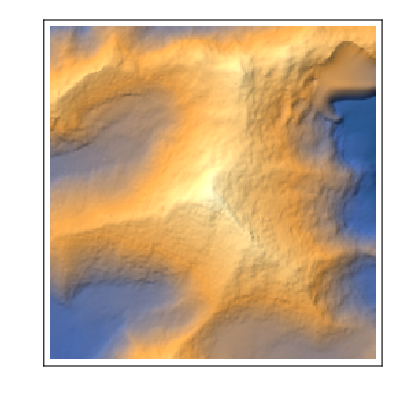

```mathematica
ReliefPlot[
	GeoElevationData[
		WolframAlphaQueryParseResults, GeoRange->Quantity[4,"Kilometers"], GeoProjection->Automatic
	]
]
(* plotting the relief of the Mount Everest *)
```

The ElevationData can have different GeoRanges. To visualize that, I create a Manipulate from which you can see the plot of the Mount Everest with different ranges varying from 2 to 20.

```mathematica
Manipulate[
	ReliefPlot[
		GeoElevationData[
			WolframAlphaQueryParseResults, GeoRange->Quantity[x,"Kilometers"], GeoProjection->Automatic 
		]
	], {x,2,20}, SaveDefinitions->True, FrameLabel->"ReliefPlot of Mount Everest with different GeoRanges"
]
(* Create a manipulate to see the mountain out of different ranges *)
```

### 10 highest mountains of each continent

I create a list of the continents in the world

```mathematica
continents = EntityList[EntityClass["GeographicRegion","Continents"]]
(* Create a list of the continents in the world *)
```

{Africa,Antarctica,Asia,Australia,Europe,North America,South America}

Then, I create a list of names (Strings) of the continents using the “Name”-Entity

```mathematica
continentsnames = Table[EntityValue[continents⟦x⟧, "Name"], {x,1,Length[continents]}]
(* Create a list of the String-names of the continents *)
```

{Africa,Antarctica,Asia,Australia,Europe,North America,South America}

Create a list of the 10 highest mountains of each continent by using the “Elevation”-EntityProperty

```mathematica
mountainsInContinent = 
	Flatten[
		Table[
			EntityList[
				EntityClass[
					"Mountain", {EntityProperty["Mountain","Continent"]-> continents⟦c⟧, EntityProperty["Mountain","Elevation"]->TakeLargest[10]}
				]
			], {c, 1, Length[continents]}
		]
	];
(* Create a list of the 10 highest mountains per continent *)
```

Create a list of the ReliefPlots of the 10 highest mountains per continent:

```mathematica
Table[
	ReliefPlot[
		GeoElevationData[
			mountainsInContinent⟦m⟧, GeoRange->Quantity[2, "Kilometers"], GeoProjection->Automatic
		]
	], {m, 1, Length[mountainsInContinent]}
];
(* Create a list of the ReliefPlots of the 10 highest mountains per continent *)
```

As you can see, a mountain (Danghar Puge) is not plotted, because there is no ElevationData avaiable. As a conclusion of not having to deal with many mountains, I just delete it from the list. I still want to have the 10 highest mountains of each continent, so I take the top 11 highest mountains and then delete one element per continent. This is the new list then :

```mathematica
mountainsInContinent= {Entity["Mountain","MountKilimanjaro"],Entity["Mountain","MountKenya"],Entity["Mountain","Mawenzi"],Entity["Mountain","MountStanley"],Entity["Mountain","MountSpeke"],Entity["Mountain","MountBakerUganda"],Entity["Mountain","MountEmin"],Entity["Mountain","MountGessi"],Entity["Mountain","MountLuigi"],Entity["Mountain","MountMeru"],Entity["Mountain","VinsonMassif"],Entity["Mountain","MountTyree::wd298"],Entity["Mountain","MountShinn::29s3h"],Entity["Mountain","GaliciaPeak::x2ftp"],Entity["Mountain","MountKirkpatrick::4857m"],Entity["Mountain","MountElizabeth::z3hd3"],Entity["Mountain","MountRutford::m2854"],Entity["Mountain","CraddockMassif::9qp6m"],Entity["Mountain","MountCraddock::964f6"],Entity["Mountain","MountEpperly::x98n7"],Entity["Mountain","MountEverest"],Entity["Mountain","K2"],Entity["Mountain","Kangchenjunga"],Entity["Mountain","Lhotse"],Entity["Mountain","KangchenjungaWest"],Entity["Mountain","YalungKang"],Entity["Mountain","KangchejungaSouth"],Entity["Mountain","Makalu"],Entity["Mountain","KangchenjungaCentral"],Entity["Mountain","LhotseMiddle"],Entity["Mountain","MountSuckling::nc945"],Entity["Mountain","MountShungol::8x9sw"],Entity["Mountain","MountVineuo::n95g3"],Entity["Mountain","MountBellamy::228g5"],Entity["Mountain","MountJagungal::74syt"],Entity["Mountain","MountLoch::832y2"],Entity["Mountain","MountHotham::k52wq"],Entity["Mountain","MountGingera::r3542"],Entity["Mountain","MountKelly::9m245"],Entity["Mountain","MountGinini::3dq98"],Entity["Mountain","MountElbrus"],Entity["Mountain","DykhTau"],Entity["Mountain","Shkhara"],Entity["Mountain","KoshtanTau"],Entity["Mountain","JangaMountain::xfn7d"],Entity["Mountain","Kazbek"],Entity["Mountain","ShotaRustaveliPeak"],Entity["Mountain","Gistola"],Entity["Mountain","Tetnuldi"],Entity["Mountain","MontBlanc"],Entity["Mountain","MountMcKinley"],Entity["Mountain","MountLogan"],Entity["Mountain","PicoDeOrizaba"],Entity["Mountain","MountSaintElias"],Entity["Mountain","Popocatepetl"],Entity["Mountain","MountForaker"],Entity["Mountain","Iztaccihuatl"],Entity["Mountain","MountLucania"],Entity["Mountain","KingPeak"],Entity["Mountain","MountSteele"],
Entity["Mountain","Aconcagua"],Entity["Mountain","OjosDelSalado"],Entity["Mountain","CerroBonete"],Entity["Mountain","MontePissis"],Entity["Mountain","Mercedario"],Entity["Mountain","Huascaran"],Entity["Mountain","NevadoTresCruces::m338f"],Entity["Mountain","Llullaillaco"],Entity["Mountain","Yerupaja"],Entity["Mountain","Tupungato"]};
```

### Create a dataset of the relief plots of the mountains

I now try again to plot the mountains, to be sure that every mountain has a GeoElevationData. This is checked by looking if there is any error message.

```mathematica
DatasetMountainsInContinent =
	Table[
		ReliefPlot[
			GeoElevationData[
				mountainsInContinent⟦m⟧, GeoRange-> Quantity[2, "Kilometers"], GeoProjection->Automatic], ImageSize->{224,224}], {m, 1, Length[mountainsInContinent]}];
(* create a list of pictures of plotted mountains out of different viewpoints and with different georanges *)
```

As there is no error, now every mountain in the list mountainsInContinent has a valid GeoElevationData.

To train a neural network, the data needs to be labeled. To do that, I create a list of all the needed labels and then create an association between SurfacePlot and label.  This association is then converted into a list.

Let n be the length of the list “DatasetMountainsInContinent” divided by the Length of the List “continentsnames”.

This means that it is the length of the number of mountains in total divided by the number of continents. This result represents how many mountains there are per country.

Each label must appear n  times in the list in succession.The order of the labels corresponds to the order of the list continentsnames, that means in an alphabetical order.

```mathematica
labelsMountainsInContinent = 
	Flatten[
		Table[
			Table[
				continentsnames⟦n⟧, (Length[DatasetMountainsInContinent]/Length[continentsnames])
			], {n,1,Length[continentsnames]}
		]
	];
(* create the list of the labels *)
```

After a list of labels is created, an association between the plots (the elements of the list “DatasetMountainsInContinent”) and the labels is needed. Afterwards the created association is converted to a list with the Normal function

```mathematica
DatasetInContinent = Normal[AssociationThread[DatasetMountainsInContinent, labelsMountainsInContinent]];
(* create the list of the association *)
```

### Create a classifier

In order to train the classifier in the best way, I will scramble the data to prevent patterns:

```mathematica
scrambledDatasetInContinent = RandomSample@DatasetInContinent;
(* scramble the data *)
```

I will split the dataset again into trainingdata and testingdata with the same proportions as in the previous example.

That means that the size of the training images will be about 75% of all the pictures, the training images for evaluation purposes are the images which remain.

```mathematica
splitSizeInContinent = Round[0.75 Length[scrambledDatasetInContinent]];
(* defining the splitSize *)
```

```mathematica
trainingDataInContinent = scrambledDatasetInContinent⟦1;;splitSizeInContinent⟧;
testingDataInContinent = scrambledDatasetInContinent⟦splitSizeInContinent;;⟧;
(* splitting the dataset into trainingdata and testing *)
```

Create a classifier that is trained on the trainingdata. Set the performanceGoal to "Quality" to achive the best results as possible:

```mathematica
cInContinent = Classify[trainingDataInContinent, PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

I now measure the performance of the trained classifier, first on the trainingdata, secondly on the testingdata and plot ConfusionMatrixes in order to see the the distribution of correctly and wrongly classified mountains. In addition to that, I return the accuracy.

ClassifierMeasurementsObject[…]

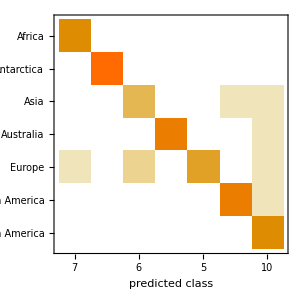
{<|Africa→0.857143,Antarctica→1.,Asia→0.666667,Australia→1.,Europe→1.,North America→0.875,South America→0.6|>,-Graphics-}

0.846154

```mathematica
cmInContinent1 = ClassifierMeasurements[cInContinent, trainingDataInContinent]
cmInContinent1[{"Precision", "ConfusionMatrixPlot"}]
cmInContinent1["Accuracy"]
```

ClassifierMeasurementsObject[…]

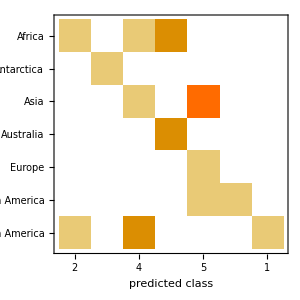
{<|Africa→0.5,Antarctica→1.,Asia→0.25,Australia→0.5,Europe→0.2,North America→1.,South America→1.|>,-Graphics-}

0.444444

```mathematica
cmInContinent2 = ClassifierMeasurements[cInContinent, testingDataInContinent]
cmInContinent2[{"Precision", "ConfusionMatrixPlot"}]
cmInContinent2["Accuracy"]
```

The results for the trainingdata and testingdata are despite of the little amount of data okay. There are some issues for example that South America, North America and the Antarctica had only one element in the test dataset. In order to fix these problems and to improve the accuracy of the classifier, it is useful to create more data.

### Create new data

I create more data by changing the GeoRange from 1 kilometers to 20 kilometers in steps of 4. In addition to that, I shift the midpoint of the ReliefPlot from 20 to 100 feet in steps of 25. That means that 4*5 = 20 pictures will be created per mountain.

```mathematica
DatasetMountainsInContinentAdd = 
	Flatten[
		Table[
			ReliefPlot[
				GeoElevationData[
					GeoRange -> Quantity[x, "Kilometer"],GeoProjection->Automatic, GeoCenter-> GeoDestination[
						(mountainsInContinent⟦m⟧["Position"]),{y,90}
					]
				]
			],{m,1,Length[mountainsInContinent]},{y,20,100,25}, {x,1,20,4}
		]
	];
(* create a list of slightly changed ReliefPlots *)
```

I create the corresponding labels in the same way I created them with the little amount of data .

```mathematica
labelsInContinentAdd = 
	Flatten[
		Table[
			Table[
				continentsnames⟦n⟧, (Length[DatasetMountainsInContinentAdd]/Length[continentsnames])
			], {n,1,Length[continents]}
		]
	];
(* create the corresponding labels for the DatasetMountainsInContinentAdd *)
```

Now, I create another list with associations of the lists “DatasetMountainsInContinentAdd” and “labelsInContinentAdd”.

```mathematica
DatasetInContinentAdd = 
	Normal[
		AssociationThread[
			DatasetMountainsInContinentAdd, labelsInContinentAdd
		]
	];
(* create a list of associations between the plots and the matching labels *)
```

I join the two created Datasets so that I have as much data as possible.

```mathematica
DatasetContinent = Join[DatasetInContinent, DatasetInContinentAdd];
(* join the two datasets *)
```

If you relaunch the kernel (e.g. close the window) you have to run the whole process again in order to get the dataset, that’s why export the created lists to a file, if you have once run the program, is often very useful. The file will be exported in your current directory.

You can get your current directory with:

```mathematica
Directory[]
(* get the current directory *)
```

Export the list “DatasetContinent” to a file in the current directory named “DatasetContinent.mx”

```mathematica
Export["DatasetContinent.mx", DatasetContinent];
(* export the list "DatasetContinent" to the file "DatasetContinent.mx" *)
```

If you now want to import the list “DatasetContinent” again, just use:

```mathematica
DatasetContinent = Import["DatasetContinent.mx"]
(* Import file "DatasetContinent.mx" in the variable DatasetContinent *)
```

### Create a classifier

To prevent any patterns, I will scramble the data.

```mathematica
scrambledDatasetContinent = RandomSample@DatasetContinent;
(* scramble the data *)
```

In order to test the real performance of the trained net, the dataset will be split into the trainingdata, with which the model will be trained and the testingdata, with which the data is tested afterwards.

I define a splitSize. It makes sense that the trainingdata is bigger than the testingdata. Normally, the value of the trainingdata is between 70% and 80% of the whole dataset,  depending, for example, on the amount of data. In this case, I’ll go with 75%:

```mathematica
splitSizeContinent = Round[0.75 * Length[scrambledDatasetContinent]];
(* defining the splitSize *)
```

Now, the data is splitted into the trainingData and testingData depending on the setted splitSize. The trainingdata goes from the beginning to the splitSize, the testingData from the splitSize to the end.

```mathematica
trainingdataContinent = scrambledDatasetContinent⟦1;;splitSizeContinent⟧;
testingdataContinent = scrambledDatasetContinent⟦splitSizeContinent;;⟧;
(* split the dataset into the trainingdata and the testingdata *)
```

Create a classifier that is trained on the trainingdata. Set the performanceGoal to “Quality” to achive the best results as possible.

```mathematica
cContinent = Classify[trainingdataContinent, PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

I measure the performance of the trained classifier, first on the trainingdata, secondly on the testingdata and plot ConfusionMatrixes in order to see the the distribution of correctly and wrongly classified mountains.

ClassifierMeasurementsObject[…]

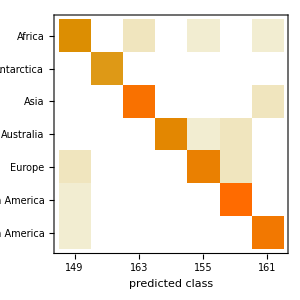
{<|Africa→0.973154,Antarctica→1.,Asia→0.98773,Australia→1.,Europe→0.987097,North America→0.975904,South America→0.981366|>,-Graphics-}

0.986201

```mathematica
cmContinent1 = ClassifierMeasurements[cContinent, trainingdataContinent]
cmContinent1[{"Precision", "ConfusionMatrixPlot"}]
cmContinent1["Accuracy"]
(* measure the performance on the trainingdata and plot a ConfusionMatrix *)
```

ClassifierMeasurementsObject[…]

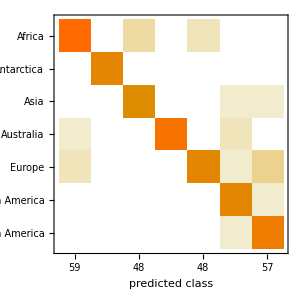
{<|Africa→0.949153,Antarctica→1.,Asia→0.9375,Australia→1.,Europe→0.958333,North America→0.901961,South America→0.894737|>,-Graphics-}

0.947658

```mathematica
cmContinent2 = ClassifierMeasurements[cContinent, testingdataContinent]
cmContinent2[{"Precision", "ConfusionMatrixPlot"}]
cmContinent2["Accuracy"]
(* measure the performance on the testingdata and plot a ConfusionMatrix *)
```

The accuracy of the trainingdata is very high and the classifier almost got everything right. The accuracy for the testingdata is also very high.

### Try the performance

You can get the probabilities for all continents for a ReliefPlot

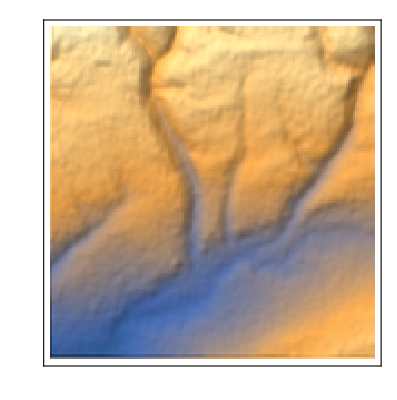
```mathematica
cContinent[-Graphics-,"Probabilities"]
(* get all the probabilities for the ReliefPlot *)
```

As an input the user can enter a code for the GeoElevationData and the program will return a GeoListPlot where the continent with the highest probability is marked.

```mathematica
input = 
	GeoElevationData[
	Entity["Mountain","Aconcagua"], GeoRange -> Quantity[2, "Kilometers"], GeoProjection-> Automatic
	]
(* input of the user *)
```

QuantityArray[…]

```mathematica
GeoListPlot[{Entity["GeographicRegion", cContinent[ReliefPlot[input]]]}]
(* Plot the most accurate continent *)
```

### Better visualization

If there is more than one possible given prediction, then mark the parts on the card. Red means the probability for this continent is 100%, black means that the probability for this continent is 0%.

```mathematica
GeoGraphics[
	{EdgeForm[Black], Flatten[
		Table[
			Style[
				Polygon[
					{Entity[
						"GeographicRegion", StringReplace[
							ToString[
								Keys[
									cContinent[ReliefPlot[input] ,"Probabilities"]
								]⟦y⟧
							], " "-> ""
						]
					]}
				], RGBColor[
					Values[
						cContinent[
							ReliefPlot[input], "Probabilities"
						]
					]⟦y⟧,0,0
				]
			],{y,Length[
				cContinent[
					ReliefPlot[input], "Probabilities"
				]
			]}
		]
	]}
]

(* first visualization *)
```

-Graphics-

Another pretty way to plot the probabilities in a map in the Wolfram Language is with GeoRegioinValuePlot

```mathematica
GeoRegionValuePlot[
	Table[
		Entity[
			"GeographicRegion", StringReplace[
				ToString[
					Keys[
						cContinent[
							ReliefPlot[input], "Probabilities"
						]
					]⟦y⟧
				], " "-> ""
			]
		]-> Values[
			cContinent[
				ReliefPlot[input], "Probabilities"
			]
		]⟦y⟧, {y, 1, Length[cContinent[ReliefPlot[input], "Probabilities"]]}
	]
]
(* second visualization *)
```

-Graphics-

### Conclusion

With this method, you can find out relatively well, the continent of the elevation data and then marks it on a world map.

To go into more detail  and to be able to predict the country would require much more data. As you have already seen in the first approach, my computing power is not sufficient for creating many graphics.

## Recognizing the mountains’ position by their elevation data

### Generating the data

First, get a list of continents in the world

```mathematica
continents = EntityList[EntityClass["GeographicRegion","Continents"]]
(* Generate a list of the continents *)
```

{Africa,Antarctica,Asia,Australia,Europe,North America,South America}

As you can see, Europe is the 5th continent in the world. As I only want to classify countries in Europe, I create a list of all the countries in Europe.

```mathematica
countriesInEurope= 
	Flatten[
		Table[
			continents⟦x⟧[EntityProperty["GeographicRegion","Countries"]], {x, 5, 5}
		]
	];
(* create a list of the countries in Europe *)
```

In addition to that, I create a list of the names of the 10 biggest countries in Europe (String)

```mathematica
countriesInEuropeNames = 
	Flatten[
		Table[
			EntityValue[
				countriesInEurope⟦x⟧, "Name"
			], {x, 1, Length[countriesInEurope]}
		]
	];
(* create a list of the names of the countries of Europe *)
```

Let' s take the 5 highest mountains per country by using the "Elevation" - EntityProperty

```mathematica
mountainsInEurope = 
	Flatten[
		Table[
			EntityList[
				EntityClass[
					"Mountain", {EntityProperty["Mountain","Countries"]->countriesInEurope⟦c⟧, EntityProperty["Mountain","Elevation"]-> TakeLargest[5]}
				]
			],{c,1,Length[countriesInEurope]}
		]
	];
(* Create a list of the 5 highest mountains per country *)
```

```mathematica
Length[countriesInEurope] * 5
```

```mathematica
Length[mountainsInEurope]
```

As you can see, the length of the mountains in Europe is not equivalent to the number of countries in Europe times 5. As a conclusion, we know, that not every country in europe has got data for its five highest mountains. Some of them don’t even have mountains for example the Vatican City.

```mathematica
mountainsInEuropeUnflatten = 
	Table[
		EntityList[
			EntityClass[
				"Mountain", {EntityProperty["Mountain","Countries"]->countriesInEurope⟦c⟧, EntityProperty["Mountain","Elevation"]-> TakeLargest[5]}
			]
		],{c,1,Length[countriesInEurope]}
	];
```

Create a dataset of the GeoElevationData of the elements in the list mountainsInEurope, using a GeoRange of 2 kilometers.

```mathematica
DatasetMountainsInEurope = 
	Table[
		Information[GeoElevationData[
			mountainsInEurope⟦m⟧, GeoRange-> Quantity[2, "Kilometers"], GeoProjection->Automatic
		],"Quantity"], {m, 1, Length[mountainsInEurope]}
	];
```

As an output, I get a couple of errors, saying that the ElevationData of some mountains is missing, This happens at some point, because Wolfram Alpha has not for every mountain the matching GeoElevationData. You can see that the errors are generated by the following mountains: Le Roissier, Pointe Luis-Amedeo, Myticas, Skolio, Cahir, Crna Glava and Strmenica.

In order to prevent the errors, I take the lists of mountains in Europe and delete the above mentioned mountains.

```mathematica
mountainsInEuropeUnflatten = 
{{Entity["Mountain","GolemiKorab"],Entity["Mountain","MajaJezerce"],Entity["Mountain","MajaBriaset::jh929"],Entity["Mountain","Gjalices"],Entity["Mountain","ZlaKolata::36p69"]},
{Entity["Mountain","PicDeComaPedrosa"],Entity["Mountain","PicDeSanfonts::979y8"],Entity["Mountain","Casamanya"],Entity["Mountain","PicDelPortVell"],Entity["Mountain","PicDelsAspres"]},
{Entity["Mountain","Grossglockner"],Entity["Mountain","Wildspitze"],Entity["Mountain","Kleinglockner::jw4s5"],Entity["Mountain","Weisskugel"],Entity["Mountain","Glocknerwand::sq282"]},
{Entity["Mountain","DzyarzhynskayaHara::59z62"]},
{Entity["Mountain","SignalDeBotrange"],Entity["Mountain","WeiszerStein::k3p2n"],Entity["Mountain","BaraqueDeFraiture::m9jng"],Entity["Mountain","CroixScaille::3ypfp"]},
{Entity["Mountain","Maglic"],Entity["Mountain","ZelenaGlava"],Entity["Mountain","Vranica"],Entity["Mountain","Lupoglav"],Entity["Mountain","Bjelasnica"]},
{Entity["Mountain","Musala"],Entity["Mountain","Vihren"],Entity["Mountain","Kutelo"],Entity["Mountain","MalkaMusala"],Entity["Mountain","BanskiSuhodol"]},
{Entity["Mountain","Dinara"],Entity["Mountain","SvetiJure"],Entity["Mountain","VaganskiVrh"],Entity["Mountain","SvetoBrdo"],Entity["Mountain","BabinVrh"]},
{Entity["Mountain","Snezka"],Entity["Mountain","LucniHora"],Entity["Mountain","StudniciHora"],Entity["Mountain","VysokeKolo"],Entity["Mountain","Praded"]},
{Entity["Mountain","YdingSkovhoj"],Entity["Mountain","Mollehoj"]},
{Entity["Mountain","SuurMunamagi::c7n7g"],Entity["Mountain","KuksinaHill::74z4b"],Entity["Mountain","MeremaeHill::h2pb9"]},
{Entity["Mountain","Slaettaratindur"],Entity["Mountain","Grafelli"],Entity["Mountain","Husareyn::hqx9f"]},
{Entity["Mountain","MountHaltia"],Entity["Mountain","Ridnitsohkka::rq7bz"],Entity["Mountain","Kovddoskaisi::8xvwh"],Entity["Mountain","Saana::tw5c7"],Entity["Mountain","Yllas::sgd9v"]},
{Entity["Mountain","MontBlanc"],Entity["Mountain","MontBlancDeCourmayeur"],Entity["Mountain","MontMaudit"],Entity["Mountain","DomeDuGouter::qfk5j"]},
{Entity["Mountain","Zugspitze"],Entity["Mountain","Hochwanner"],Entity["Mountain","Hollentalspitzen::t9km4"],Entity["Mountain","Watzmann"],Entity["Mountain","Hochblassen::2vbq9"]},
{Entity["Mountain","RockGibraltar"],Entity["Mountain","MiddleHill::3rtdv"]},
{Entity["Mountain","MountOlympusGreece"],Entity["Mountain","Smolikas"],Entity["Mountain","Kajmakcalan::9fpxd"]},
{},
{Entity["Mountain","Kekes"],Entity["Mountain","Csovanyos::523kx"],Entity["Mountain","Zengo"],Entity["Mountain","Csobanc::m44rd"]},
{Entity["Mountain","Hvannadalshnukur"],Entity["Mountain","Herethubreieth"],Entity["Mountain","Eyjafjallajokull"],Entity["Mountain","KerlingInIceland::8x8td"],Entity["Mountain","Esjufjoll"]},
{Entity["Mountain","Carrantuohill"],Entity["Mountain","Beenkeragh::2v5y6"],Entity["Mountain","CaherMountain::f9qkr"],Entity["Mountain","CnocNaPeiste::sv74q"]},
{Entity["Mountain","Snaefell"],Entity["Mountain","NorthBarrule::532k9"],Entity["Mountain","Beinn-y-Phott::936f2"],Entity["Mountain","SlieauFreoaghane::62t88"],Entity["Mountain","SouthBarrule::t572k"]},
{Entity["Mountain","MontBlanc"],Entity["Mountain","MontBlancDeCourmayeur"],Entity["Mountain","MonteRosa"],Entity["Mountain","Nordend"],Entity["Mountain","Zumsteinspitze"]},
{Entity["Mountain","LesPlatons::x84dq"]},
{Entity["Mountain","Djeravica"],Entity["Mountain","MajaEZeze::8595t"],Entity["Mountain","Hajla::k5742"],Entity["Mountain","MajaBogicaj::psdx4"],Entity["Mountain","MokraGoraMountain::3852j"]},
{Entity["Mountain","Gaizins"]},
{Entity["Mountain","Grauspitz"],Entity["Mountain","Naafkopf"],Entity["Mountain","Falknis"],Entity["Mountain","Augstenberg::q9zft"],Entity["Mountain","Plasteikopf::mzx7t"]},
{Entity["Mountain","AukstojasHill::jjj2b"],Entity["Mountain","Juozapine"],Entity["Mountain","Kepaluskalnis::g5yfr"]},
{Entity["Mountain","Kneiff"],Entity["Mountain","Buurgplaatz"]},
{Entity["Mountain","GolemiKorab"],Entity["Mountain","TitovVrv"],Entity["Mountain","Pelister"],Entity["Mountain","SolunskaGlava"],Entity["Mountain","Ljuboten"]},
{Entity["Mountain","TaDmejrek::52ws4"],Entity["Mountain","GebelSanPietru::gwg6y"]},
{},
{Entity["Mountain","MontAgel"]},
{Entity["Mountain","Djeravica"],Entity["Mountain","ZlaKolata::36p69"],Entity["Mountain","KolataEMire::78knk"],Entity["Mountain","BobotovKuk"],Entity["Mountain","ZljebMountain::227gm"]},
{Entity["Mountain","Scenery"],Entity["Mountain","Vaalserberg"],Entity["Mountain","Vrouwenheide::947yh"],Entity["Mountain","MountSaintPeter::4vgnc"]},
{Entity["Mountain","Galdhoppigen"],Entity["Mountain","Glittertind"],Entity["Mountain","StoreSkagastolstind"],Entity["Mountain","StoreStyggedalstind"],Entity["Mountain","Skarstind"]},
{Entity["Mountain","Rysy"],Entity["Mountain","Swinica"],Entity["Mountain","KoziWierch"],Entity["Mountain","StarorobocianskiWierch"],Entity["Mountain","Koscielec"]},
{Entity["Mountain","MontanhaDoPico"],Entity["Mountain","Torre::mpq22"],Entity["Mountain","SerraDaEstrela"],Entity["Mountain","CantaroMagro"],Entity["Mountain","PicoRuivo::rmk98"]},
{Entity["Mountain","Moldoveanu"],Entity["Mountain","Negoiu"],Entity["Mountain","VisteaMare"],Entity["Mountain","Lespezi"],Entity["Mountain","ParangulMare"]},
{Entity["Mountain","MountElbrus"],Entity["Mountain","DykhTau"],Entity["Mountain","JangaMountain::xfn7d"],Entity["Mountain","ShotaRustaveliPeak"],Entity["Mountain","MountDzhimara::m84gf"]},
{Entity["Mountain","MonteTitano::nqf5k"]},
{Entity["Mountain","Djeravica"],Entity["Mountain","BobotovKuk"],Entity["Mountain","Midzor"]},
{Entity["Mountain","Gerlach"],Entity["Mountain","GerlachovskaVeza::8by3f"],Entity["Mountain","LomnickyStit"],Entity["Mountain","LadovyStit::sny8n"],Entity["Mountain","Krivan"]},
{Entity["Mountain","Triglav"],Entity["Mountain","Skrlatica"],Entity["Mountain","Mangart"],Entity["Mountain","VisokiRokav"],Entity["Mountain","Jalovec"]},
{Entity["Mountain","PicoDeTeide"],Entity["Mountain","MuleyHacen"],Entity["Mountain","PicoDAneto"],Entity["Mountain","PicoVeleta"],Entity["Mountain","PicoDePosets"]},
{Entity["Mountain","Newtontoppen"],Entity["Mountain","Perriertoppen::sr9tz"],Entity["Mountain","Ceresfjellet::s4kpb"],Entity["Mountain","Chadwickryggen::m2699"],Entity["Mountain","Galileotoppen::258z4"]},
{Entity["Mountain","Kebnekaise"],Entity["Mountain","Sarektjkk"],Entity["Mountain","Kaskasatjakka::2z584"],Entity["Mountain","Ahkka::fsy5v"],Entity["Mountain","Kaototjaokko"]},
{Entity["Mountain","MonteRosa"],Entity["Mountain","Dunantspitze::b532d"],Entity["Mountain","Grenzgipfel::vc8cs"],Entity["Mountain","Nordend"],Entity["Mountain","Zumsteinspitze"]},
{Entity["Mountain","Goverla"],Entity["Mountain","Brebeneskul::g88h7"],Entity["Mountain","ChornaGora"],Entity["Mountain","PetrosInChornohora::3578x"],Entity["Mountain","HutynTomnatyk::zjtd5"]},
{Entity["Mountain","BenNevis"],Entity["Mountain","BenMacdui"],Entity["Mountain","Braeriach"],Entity["Mountain","CairnToul::4n73v"],Entity["Mountain","Cairngorm"]},
{}};
(* new list of mountains in Europe where GeoElevationData is avaiable *)
```

Update the list mountainsInEurope which is the flattened list of the list mountainInEuropeUnflatten

```mathematica
mountainsInEurope = Flatten@mountainsInEuropeUnflatten;
(* flattened list of the mountains in Europe *)
```

I can now try again to plot the mountains to be sure that now every mountain in the list has an GeoElevationData

```mathematica
DatasetMountainsInEurope = 
	Table[
		GeoElevationData[
			mountainsInEurope⟦m⟧, GeoRange-> Quantity[2, "Kilometers"], GeoProjection->Automatic
		]["Magnitudes"], {m, 1, Length[mountainsInEurope]}
	];
(* create a list of the GeoElevationData of the mountains in Europe *)
```

There was no error, so every mountain in this list has a valid EvaluationData.

### Create a labeled dataset

To train a neural network, the data needs to be labeled. Because of that, I create a list of labels and then create an association between the label-list and the GeoElevationData-list and convert this association into a list.

I cannot use the method from above to create the labels, because there is not the same number per mountains per country.

I first create an empty list for the labels and then walk through the unflatted list of mountains in Europe step by step. The elements in the same sublist belong to the same country, that means that they have the same label. Step by step I look at each sublist. In each sublist, I create as many labels for the countrys as there are elements in teh sublist. It is important to know that the nth sublist belong to the nth country. I do this by a for-loop. Some countrys don’t have any elements, so by counting the elements in the sublist and then creating that many labels, it is possible that one country doesn’t have a label. This is no problem though, because there is not an element in the ElevationDataList for it, too.

```mathematica
labelsMountainsInEurope = {}; 
For[
	i=1, i<=Length[mountainsInEuropeUnflatten], i++,
	If[
		mountainsInEuropeUnflatten⟦i⟧≠ {},
		For[
			j=1, j<=Length[mountainsInEuropeUnflatten⟦i⟧], j++,
			AppendTo[labelsMountainsInEurope, countriesInEuropeNames⟦i⟧]
		]
	]
] 
(* create a list of labels in the same order as the elements in the mountainsInEurope-list *)
```

Now, I create an association between the list DatasetMountainsInEurope and the list of the labels called labelsMountainsInEurope and then convert it into a list.

```mathematica
DatasetInEurope = 
	Normal[
		AssociationThread[
			DatasetMountainsInEurope, labelsMountainsInEurope
		]
	];
(* create a list of associations between the ElevationData and its labels *)
```

I only have a maximal number of 5 mountains per country (some countrys even just 1!). This amount of data is not big enough to train a classifier. As a result, new data is required, which I have to create.

I create the new data by changing the GeoRange from 1 kilometers to 20 kilometers in steps of 4 and changing the center of the picture by shifting it in a range from 20 feet to 100 feet to the east in steps of 20 This means, that per mountain an amount of 5 * 5 = 25 different GeoElevationData will be created. This is enough to train the Classifier.

Because of the high number of mountains, I don’t want to download the GeoElevationData every time new, but just changing the GeoCenter and the GeoRange from the unique downloaded GeoElevationData. In addition to that, every created GeoElevationData is saved into a directory. If there is already a file that is named in that way, the program won’t create another one and leave this one. In the case of a mountain that doesn’t have GeoElevationData, I catch the error with the functions Quiet and Check with the parameter of an empty list {}. In addition to that, I monitor the current values of y, x and m to see how fast the program is running.

```mathematica
Block[{geo}, 
	Table[
		With[
			{filename = ToString@x<>"-"<>ToString[y]<>"-"<>ToString[m]<>".mx"},
			If[
				!FileExistsQ[filename], 
				geo = Quiet[
					Check[
						GeoElevationData[
							GeoRange -> Quantity[x, "Kilometer"],GeoProjection->Automatic, GeoCenter -> GeoDestination[(mountainsInEurope⟦m⟧["Position"]),{y,90}]
						],{}
					]
				];
			DumpSave[filename, geo]
			]
		];,{y,20,100,20}, {x,1,20,4},{m,1,Length[mountainsInEurope]}
	]
]~Monitor~{y,x, m};
```

After that, a list is created of the GeoElevationData by taking the files and adding them to the list.  If you look at the AbsoluteTiming, you can see that this method is much faster than the earlier approches.

```mathematica
DatasetMountainsInEuropeAdd = 
	Block[
		{geo},Table[
			If[MatchQ[ToExpression/@StringSplit[FileBaseName[f], "-"], 
			{Alternatives@@Range[1,20,4], Alternatives@@Range[20,100,20], _}],
			 Get[f]; geo,Nothing], {f, FileNames["*-*-*.mx"]}
		]
	]~Monitor~f; //AbsoluteTiming
(* Create a list of the different GeoElevationData of mountains *)
```

Now, I export the data so if the kernel is relaunched I still have this dataset.

```mathematica
Export["datasetMountainsInEuropeAdd.mx",DatasetMountainsInEuropeAdd];
(* Export the data *)
```

Remember that it will be saved in your current Directory, which you get with :

```mathematica
Directory[]
(* get the current directory *)
```

Import the file if the kernel was relaunched:

```mathematica
DatasetMountainsInEuropeAdd = Import["datasetMountainsInEuropeAdd.mx"];
(* Import the DatasetMountainsInEuropeAdd *)
```

In order to get the whole associated dataset, I have to create labels in the same order. As mentioned earlier, you can’t create the labels in the earlier ways, because there is not an equal number of mountains per country. By creating the DatasetMountainsInEuropeAdd, I used the Table function with the last parameter of the mountain. That means that the order of the countrys occurs repeatedly. A copy of this repeated order corresponds to the order of the already created label list.

As a conclusion, I can create the new labels, by looking at the number how often the order is repeated and then adding the previously created list that often in a row.

```mathematica
labelsMountainsInEuropeAdd = 
	Flatten[
		Table[
			labelsMountainsInEurope, (Length[DatasetMountainsInEuropeAdd] / Length[labelsMountainsInEurope])
		]
	];
(* Create a list of the labels corresponding to the EvaluationData of the list DatasetMountainsInEuropeAddFlatten *)
```

### Creating and training the classifier

Let’s look at the Length of the Dataset:

```mathematica
Length[DatasetInEuropeAdd]
(* get the length of the full dataset *)
```

It' s 4550 long. This is enough for the Neural Network. I split the data into two parts. Therefore I create a list of the positions of the trainingdata in the dataset and the positions of the testdata. These will be chosen randomly. Furthermore, I define that there are 2825 elements in the trainingset.

```mathematica
trainingpos = RandomSample[Range[Length[DatasetMountainsInEuropeAdd]], 2825];
testpos = Complement[Range[Length[DatasetMountainsInEuropeAdd]], trainingpos];
```

I export the trainingset, the testset and the matching labels. Therefore, I call the positions on the dataset, so that the real ElevationData is exported.

```mathematica
Export["trainingset.mx", DatasetMountainsInEuropeAdd[[trainingpos]]];
Export["testset.mx", DatasetMountainsInEuropeAdd[[testpos]]];
Export["trainingsetoutcome.mx", labelsMountainsInEuropeAdd[[trainingpos]]];
Export["testsetoutcome.mx", labelsMountainsInEuropeAdd[[testpos]]];
(* export the sets with labels *)
```

QuantityArray[…] 
This is the structure of an element of the trainingset. As you can see, it has an unity, which I don’t need, that’s why I create a trainingset without units using the function QuantityMagnitude

```mathematica
Export["trainingsetWithoutUnit.mx", QuantityMagnitude[trainingset]];
```

Now, I relaunch my kernel to delete a lot of unnecessary memory. 
After that, I need to import the important files again. Don’t forget to run the function in Settings again.

```mathematica
trainingset = Import["trainingsetWithoutUnit.mx"]; 
trainingsetOutcome = Import["trainingsetoutcome.mx"]; 
(* import the important sets *)
```

Let us doublecheck if the data and their labels have the same length

```mathematica
Length/@ {trainingset, trainingOutcome}
```

They both have the size 1825.

Now, I rescale the array, that means that every value is between 0 and 1 and create an image out of it

```mathematica
itrain = Image/@ Rescale[trainingset];
```

Now we can call the Classifier and train it using RandomForest as method

```mathematica
cEurope = Classify[itrain -> trainingsetOutcome, PerformanceGoal->"Quality", Method->"RandomForest"]
```

```mathematica
ClassifierFunction[…]
```

Let' s test it now : 
Therefore, I have to first Import my testset and my testsetOutcome

```mathematica
testset = Import["testset.mx"];
testsetOutcome = Import["testsetoutcome.mx"];
(* import test files *)
```

Before I can use the testdata, I have to change it. I start with deleting the Unity, going on with Clipping it to prevent errors and then rescale it and form it into an image. This needs to be done, because the neural network was trained on this datatype:

```mathematica
itestset=Image/@Rescale[Clip[QuantityMagnitude[testset],MinMax[trainingset]],MinMax[trainingset]];
```

To use the Network again if the kernel has been relaunched, but you don’t want to do training anymore, I exported the classifier

```mathematica
Export["cEurope.mx", cEurope];
```

I look at the measurements of the classifier and export them, too:

```mathematica
cm = ClassifierMeasurements[cEurope, itestset -> testsetOutcome];
Export["cm.mx", cm];
```

I have a look at the ConfusionMatrix now:

```mathematica
cm["ConfusionMatrixPlot"]
```

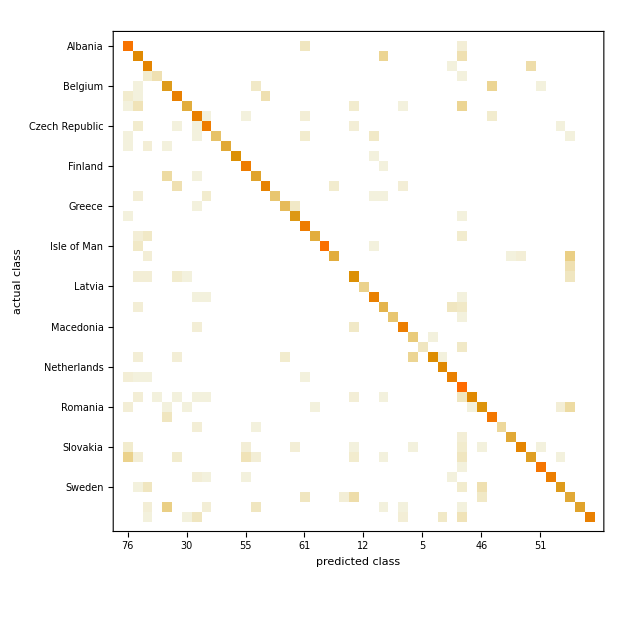

We get the accuracy with:

```mathematica
cm["Accuracy"]
```

```mathematica
0.784
```

And I can see the Accuracy for every country individually

```mathematica
cm["Precision"]
```

```mathematica
<|"Albania"->0.6578947368421053,"Andorra"->0.5507246376811594,"Austria"->0.6507936507936508,"Belarus"->0.875,"Belgium"->0.5245901639344263,"Bosnia and Herzegovina"->0.7166666666666667,"Bulgaria"->0.9,"Croatia"->0.7166666666666667,"Czech Republic"->0.8333333333333334,"Denmark"->1.,"Estonia"->1.,"Faroe Islands"->1.,"Finland"->0.8181818181818182,"France"->0.7142857142857143,"Germany"->0.857142857142857,"Gibraltar"->1.,"Greece"->0.875,"Hungary"->0.8461538461538461,"Iceland"->0.7377049180327869,"Ireland"->0.9642857142857143,"Isle of Man"->1.,"Italy"->0.9,"Jersey"->0.,"Kosovo"->0.603448275862069,"Latvia"->1.,"Liechtenstein"->0.86,"Lithuania"->0.6,"Luxembourg"->1.,"Macedonia"->0.88,"Malta"->0.5555555555555556,"Monaco"->1.,"Montenegro"->0.972972972972973,"Netherlands"->0.8837209302325582,"Norway"->0.86,"Poland"->0.47413793103448276,"Portugal"->0.9743589743589743,"Romania"->0.7391304347826086,"Russia"->0.7741935483870968,"San Marino"->1.,"Serbia"->0.9655172413793104,"Slovakia"->0.9534883720930233,"Slovenia"->0.7948717948717948,"Spain"->0.9607843137254902,"Svalbard"->1.,"Sweden"->0.8888888888888888,"Switzerland"->0.4444444444444444,"Ukraine"->1.,"United Kingdom"->1.|>
```

### Visualization

```mathematica
input = 
	GeoElevationData[
	Entity["Mountain","BenNevis"], GeoRange -> Quantity[2, "Kilometers"], GeoProjection-> Automatic
	]
input = Image[Rescale[QuantityMagnitude[input]]]
```

QuantityArray[…]

-Graphics-

Now, I can plot the corresponding map

```mathematica
GeoRegionValuePlot[
	Table[
		Entity[
			"Country", StringReplace[
				ToString[
					Keys[
						cEurope[input, "Probabilities"
						]
					]⟦y⟧
				], {" "-> "", "BosniaandHerzegovina"-> "BosniaHerzegovina", "IsleofMan"-> "IsleOfMan"}
			]
		]-> Values[
			cEurope[input, "Probabilities"
			]
		]⟦y⟧, {y, 1, Length[cEurope[input, "Probabilities"]]}
	]
]
```